Initialize functions

```mathematica
(*Ensure that variables are defined globally*)
SetOptions[EvaluationNotebook[],CellContext->"Global`"]
NotebookOpen[NotebookDirectory[]<>"GB-strain-scattering_init.nb"];
NotebookEvaluate[NotebookDirectory[]<>"GB-strain-scattering_init.nb"];
```

Define material values and phonon dispersion parameters

```mathematica
(*#############################*)
(*### Material values for Si ###*)
(*#############################*)

(*#### crystal properties ####*)
vs=6084. (*[m/s] average speed of sound*);
V=2*10^-29 (*[m^3] volume of atom*);
n=2(*# atoms per primitive unit cell (N in paper)*);
γ=1(*Gruneissen parameter*);
ν=0.27(*Poisson's ratio*);
kmax=k0[V*n]//N(*[m^-1] edge of FBZ*);
ωD=vs kmax(*[s^-1] Debye frequency*);
disp="Debye";
ωk[k_]:=vs k (*Debye dispersion relation*);
vg[k_]:=vs (*phonon group velocity*);

(*#### phonon-phonon ####*)
C1=2.69*10^-19 (*[s/K]*);
C2=167(*[K]*);

(*#### point defect ####*)
C3=1.81*10^-45 (*[s^3]*);

(*#### microstructure ####*)
b=(V n)^(1/3)(*[m] Burger's vector*);
dGS=350*10^-9 (*[m] average grain size*);
n1D=3/dGS//N(*[m^-1] number density of GBs *);
d=3*10^-9 (*[m] GB dislocation spacing (D in paper)*);
```

Diffraction peaks in Γ_gbs(k)

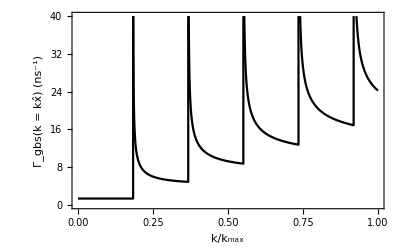

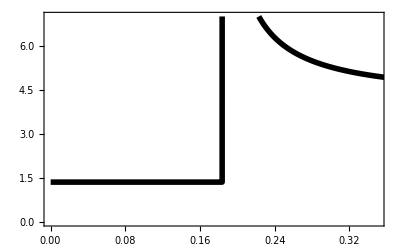

```mathematica
ΓMakeList[θ_,ϕ_]:=Table[{ω/ωD,ΓGBS[ω/vs,θ,ϕ]*10^-9},{ω,0,ωD,10^10}];
(*θ=π/2 ϕ=0 is phonon incident normal to the GB.*)
ΓlistGBS=ΓMakeList[π/2,0];

ListPlot[{ΓlistGBS},
PlotStyle->{Black},
PlotRange->{{0,1},{0,40}},
Joined->True,
FrameLabel->{"k/k_max","Γ_gbs(k = kx̂) (ns^-1)"}]

ListPlot[{ΓlistGBS},
Joined->True,
FrameStyle->Directive[FontFamily->"Times New Roman",FontSize->20,Black],
PlotStyle->Directive[Black,Thickness[0.01]],
PlotRange->{{0,0.35},{0,7}}]
```

Calculating (τ_gbs(ω))^-1

```mathematica
τGBSθϕIntegrate[ωD/(vs * 10) ,90]
```

```mathematica
(*A convergence test was perfomed on δk by caluclating κL at different δk. δk=2*10^8 was found to be fully converged. This calculation takes ~20 min on most personal computers*)
Clear[d]
τGBSList={disp};
δk=2.*10^8;
For[d=1.0*10^-9,d≤8.0*10^-9,d=d*2.0,
Print[d];
τGBSListd=Table[{ω/vs,τGBSθϕIntegrate[ω/vs,90]},{ω,vs δk,ωD,vs δk}];
AppendTo[τGBSList,{d,θcalc[b,d],τGBSListd}]
]
```

1.×10^-9

2.×10^-9

4.×10^-9

8.×10^-9

```mathematica
τGBSθϕIntegrate[ωD/(2* vs),90]
```

```mathematica
(*############################*)
(*#### Exports τGBS results ###*)
(*############################*)
Export[NotebookDirectory[]<>"../Results/tauSTGB_results.m",τGBSList]
```

/Users/rileyhanus/Desktop/Papers/Phonon_diffraction/Scripts/FOR_DISTRIBUTION/Phonon-scattering-and-transport-in-polycyrstals/core/../Results/tauSTGB_results.m

```mathematica
(*##############################################*)
(*#### Imports the last exported τGBS result ####*)
(*##############################################*)
τGBSList=Import[NotebookDirectory[]<>"../Results/tauSTGB_results.m"];
```

Plotting τ_gbs(ω) for a STGB

STGB

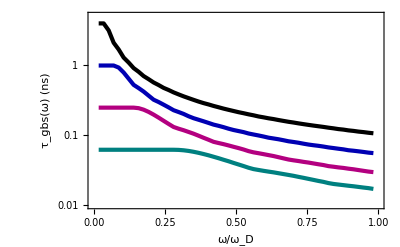

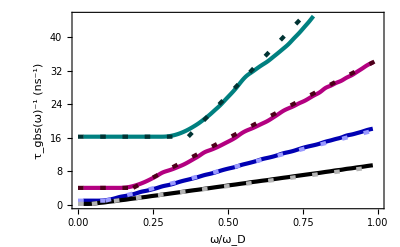

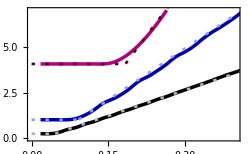

```mathematica
"STGB"
Show[ListLogPlot[{τGBExtract[τGBSList,2],
τGBExtract[τGBSList,3],τGBExtract[τGBSList,4],τGBExtract[τGBSList,5]},
PlotStyle->{Directive[RGBColor[0.,0.5,0.5],Thickness[0.0075]],
Directive[RGBColor[0.7,0.,0.5],Thickness[0.0075]],
Directive[RGBColor[0.,0,0.7],Thickness[0.0075]],
Directive[Black,Thickness[0.0075]]},
FrameLabel->{Style["ω/ω_D",16],Style["τ_gbs(ω) (ns)",16]},
PlotRange->{{0,1},{0.01,5}},
Joined->True,
PlotRange->All]]
Show[
ListPlot[{ΓGBExtract[τGBSList,2],
ΓGBExtract[τGBSList,3],ΓGBExtract[τGBSList,4],ΓGBExtract[τGBSList,5]},
PlotStyle->{Directive[RGBColor[0.,0.5,0.5],Thickness[0.0075]],
Directive[RGBColor[0.7,0.,0.5],Thickness[0.0075]],
Directive[RGBColor[0.,0,0.7],Thickness[0.0075]],
Directive[Black,Thickness[0.0075]]},
FrameLabel->{Style["ω/ω_D",16],Style["τ_gbs(ω)^-1 (ns^-1)",16]},
PlotRange->{{0,1},{0,45}},
Joined->True,
InterpolationOrder->3,
PlotRange->All],
Plot[{τinvEmp[ω*ωD,1*10^-9,b,n1D]*10^-9,τinvEmp[ω*ωD,2*10^-9,b,n1D]*10^-9,τinvEmp[ω*ωD,4*10^-9,b,n1D]*10^-9,τinvEmp[ω*ωD,8*10^-9,b,n1D]*10^-9},{ω,0,1},
PlotStyle->{Directive[Dashing[{.01,0.03}],RGBColor[0,0.2,0.2],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.3,0.,0.1],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.6,0.6,1],Thickness[0.0075]],
Directive[Dashing[{.01,0.03}],GrayLevel[0.7],Thickness[0.0075]]}]]

Show[
ListPlot[{ΓGBExtract[τGBSList,2],ΓGBExtract[τGBSList,3],
ΓGBExtract[τGBSList,4],ΓGBExtract[τGBSList,5]},
PlotStyle->{Directive[RGBColor[0.,0.5,0.5],Thickness[0.01]],
Directive[RGBColor[0.7,0.,0.5],Thickness[0.01]],
Directive[RGBColor[0.,0,0.7],Thickness[0.01]],
Directive[Black,Thickness[0.01]]},
FrameLabel->{Style["",16],Style["",16]},
PlotRange->{{0,0.4},{0,7}},
ImageSize->250,
Joined->True,
InterpolationOrder->3,
PlotRange->All],
Plot[{τinvEmp[ω*ωD,1*10^-9,b,n1D]*10^-9,τinvEmp[ω*ωD,2*10^-9,b,n1D]*10^-9,τinvEmp[ω*ωD,4*10^-9,b,n1D]*10^-9,τinvEmp[ω*ωD,8*10^-9,b,n1D]*10^-9},{ω,0,1},
PlotStyle->{Directive[Dashing[{.01,0.03}],RGBColor[0,0.2,0.2],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.3,0.,0.1],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.6,0.6,1],Thickness[0.0075]],
Directive[Dashing[{.01,0.03}],GrayLevel[0.7],Thickness[0.0075]]}]]
```

Convert τ(ω) to t(ω) and plot

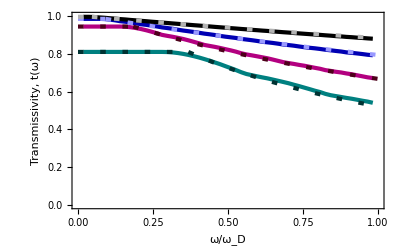

```mathematica
Show[ListPlot[{tGBExtract[τGBSList,2],tGBExtract[τGBSList,3],
tGBExtract[τGBSList,4],tGBExtract[τGBSList,5]},
PlotRange->{{0,1},{0.,1}},
FrameLabel->{"ω/ω_D","Transmissivity, t(ω)"},
Joined->True,
PlotStyle->{Directive[RGBColor[0.,0.5,0.5],Thickness[0.0075]],
Directive[RGBColor[0.7,0.,0.5],Thickness[0.0075]],
Directive[RGBColor[0.,0,0.7],Thickness[0.0075]],
Directive[Black,Thickness[0.0075]]}],Plot[{tEmp[ω*ωD,1*10^-9,b,n1D],tEmp[ω*ωD,2*10^-9,b,n1D],tEmp[ω*ωD,4*10^-9,b,n1D],tEmp[ω*ωD,8*10^-9,b,n1D]},{ω,0,1},
PlotStyle->{Directive[Dashing[{.01,0.03}],RGBColor[0,0.2,0.2],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.3,0.,0.1],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.6,0.6,1],Thickness[0.0075]],
Directive[Dashing[{.01,0.03}],GrayLevel[0.7],Thickness[0.0075]]}]]
```

Calculating κ_L

```mathematica
Timing[
κTList={disp};
For[i=2,i≤ 5,i++,
Print[τGBSList[[i,1]]//N];
κT={};
For[T=5,T≤ 500,T=T*1.1,
AppendTo[κT,{T,κLCalc[τTotCalc[τGBSList[[i,3]],T],T]}]];
AppendTo[κTList,{τGBSList[[i,1]]//N,τGBSList[[i,2]],κT}]]]
```

1.×10^-9

2.×10^-9

4.×10^-9

8.×10^-9

{0.28003,Null}

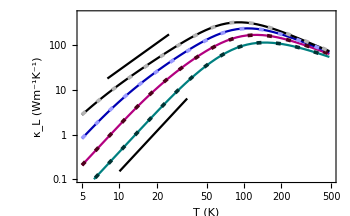

```mathematica
Show[ListLogLogPlot[{κTList[[2,3]],κTList[[3,3]],κTList[[4,3]],κTList[[5,3]]},
FrameLabel->{Style["T (K)"],Style["κ_L (Wm^-1K^-1)",SingleLetterItalics->False]},
FrameTicks->Automatic,
Joined->True,
PlotStyle->{RGBColor[0.,0.5,0.5],RGBColor[0.7,0.,0.5],RGBColor[0.,0,0.7],Black},
PlotRange->{{5,500},{0.1,500}},
ImageSize->350],
LogLogPlot[{κL[T,(τinvEmp[ω,1*10^-9,b,n1D]+τppModel[ω,T,C1,C2]^-1+τPD[ω,C3]^-1)^-1,vs,ω/vs,{ω,0,ωD}],κL[T,(τinvEmp[ω,2*10^-9,b,n1D]+τppModel[ω,T,C1,C2]^-1+τPD[ω,C3]^-1)^-1,vs,ω/vs,{ω,0,ωD}],κL[T,(τinvEmp[ω,4*10^-9,b,n1D]+τppModel[ω,T,C1,C2]^-1+τPD[ω,C3]^-1)^-1,vs,ω/vs,{ω,0,ωD}],κL[T,(τinvEmp[ω,8*10^-9,b,n1D]+τppModel[ω,T,C1,C2]^-1+τPD[ω,C3]^-1)^-1,vs,ω/vs,{ω,0,ωD}]},{T,5,500},
PlotStyle->{Directive[Dashing[{.01,0.03}],RGBColor[0,0.2,0.2],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.3,0.,0.1],Thickness[0.0075]],Directive[Dashing[{.01,0.03}],RGBColor[0.6,0.6,1],Thickness[0.0075]],
Directive[Dashing[{.01,0.03}],GrayLevel[0.7],Thickness[0.0075]]}],
ListLogLogPlot[{T2[18,{Tref,8,25}],T3[0.15,{Tref,10,35}]},Joined->True]]
```

```mathematica
LineLegend[{Directive[Black,Thickness[0.0075]],Directive[RGBColor[0.,0,0.7],Thickness[0.0075]],
Directive[RGBColor[0.7,0.,0.5],Thickness[0.0075]],Directive[RGBColor[0.,0.5,0.5],Thickness[0.0075]]},
{Style["     8        2",FontFamily->"Times New Roman",18],Style["     4        5",FontFamily->"Times New Roman",18],Style["     2        10",FontFamily->"Times New Roman",18],Style["     1        19",FontFamily->"Times New Roman",18]},Spacings->0.3]
```

Supplemental: 
Pole plots of Γ^-1(k)

k=1π/d

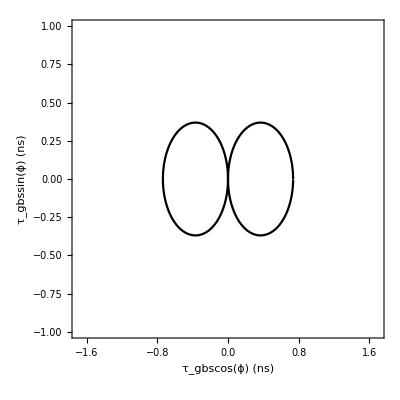

k=2π/d

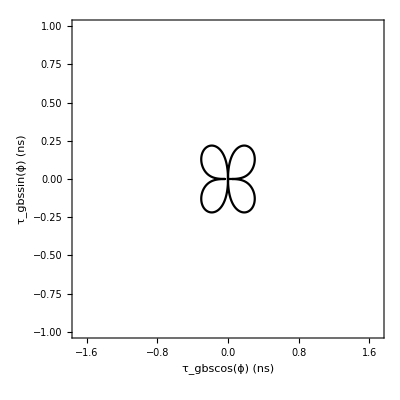

k=3π/d

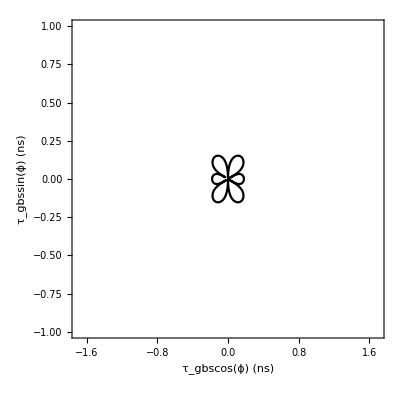

k=4π/d

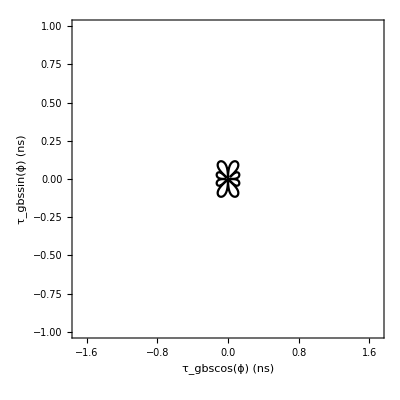

```mathematica
d=3*10^-9;
For[i=1,i≤4,i++,
Print["k="<>ToString[i]<>"π/d"];
Print[τPolarPlot[i π/d]]]
```